# QFT compilation

## Toy device

Connectivity

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

Modules

```mathematica
(*Test for the variety of the initial states *)
checkVariation[dev_,unitary_,ntrainstates_]:=Module[{conf,a},
conf=DefaultConfig[dev,unitary,ntrainstates];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
(*Print[i,":",a];*)
ToString[Reverse@Sort[Length/@a]]
]

checkedConf[dev_,unitary_,ntrainstates_]:=Module[{conf,a},
While[True,
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,ntrainstates];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]
```

```mathematica
SetAttributes[CompileCirc,HoldAll]
CompileCirc[conf_,unitary_,qubitsnum_]:=Module[{nansatz,simpncirc,fdist,ρ,qubits,ancillas,bells,ψ,uqubits},

{time,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}}=Timing[CircuitSynthesis[qubitsnum,conf]];

nansatz=noisyAnsatz[ansatz/.θvars,conf];
simpncirc=SimplifyCircuit[DeleteCases[DeleteCases[nansatz,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
(* Fidelity distance *)
ρ=CreateDensityQureg[qubitsnum*2];
ψ=CreateQureg[qubitsnum*2];
uqubits=Range[0,-1+IntegerPart[Log2@Length@unitary]];
qubits=Range[0,qubitsnum-1];
ancillas=Range[qubitsnum,qubitsnum*2-1];
bells=Flatten[{Subscript[H, #[[1]]],Subscript[C, #[[1]]][Subscript[X, #[[2]]]]}&/@(Transpose[{qubits,ancillas}])];
ApplyCircuit[ρ,bells];
ApplyCircuit[ψ,bells];
ApplyCircuit[ρ,{Subscript[U, Sequence@@uqubits][ConjugateTranspose@unitary]}];
ApplyCircuit[ρ,simpncirc];

fdist=CalcFidelity[ρ,ψ];
DestroyQureg[ρ];
DestroyQureg[ψ];

Print["compile time:",time/3600," hours; total iterations ",fev];
Print@ListPlot[Elist,AxesLabel->{"Successful iteration","Cost"}];
Print@DrawCircuit[ansatz,qubitsnum];
Print["prob(0):",probzeros];
Print["dist_fid=",fdist]
]
```

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

## 3 qubit QFT

```mathematica
qubitsnum=3;
```

```mathematica
Graph[Range[0,qubitsnum-1],Table[j<->j+1,{j,0,qubitsnum-2}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

-Graphics-

## Clean device

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->40,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.999,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{0,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.999,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{0,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->10
};
```

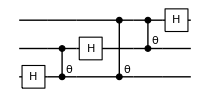

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

Compilation with automatically generated ansatz

@cycle1:Fri 16 Sep 2022 14:55:56, fev:337, <E>: 0.30512894325461587 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 0, 6}

@cycle2:Fri 16 Sep 2022 14:59:08, fev:572, <E>: 0.1606147173236766 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 0, 8}

@cycle3:Fri 16 Sep 2022 15:03:14, fev:922, <E>: 0.1219816795246205 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 40, 0, 0, 11}

@cycle4:Fri 16 Sep 2022 15:06:09, fev:1077, <E>: 0.09274187234592178 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 50, 0, 0, 14}

@cycle5:Fri 16 Sep 2022 15:11:02, fev:1392, <E>: 0.08344007630972801 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 63, 0, 0, 17}

@cycle6:Fri 16 Sep 2022 15:15:25, fev:1572, <E>: 0.07083232355631906 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 71, 0, 0, 17}

@cycle7:Fri 16 Sep 2022 15:23:25, fev:1927, <E>: 0.06845779041997112 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 81, 0, 0, 19}

@cycle8:Fri 16 Sep 2022 15:28:22, fev:2160, <E>: 0.0660177611114386 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 95, 0, 0, 19}

@cycle9:Fri 16 Sep 2022 15:35:06, fev:2374, <E>: 0.06081457353008599 nansatz: 34 merged-smallθ-metric-bf-gmerged: {0, 102, 0, 0, 20}

@cycle10:Fri 16 Sep 2022 15:42:00, fev:2579, <E>: 0.05971110109902269 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 112, 0, 0, 21}

@cycle11:Fri 16 Sep 2022 15:51:16, fev:2853, <E>: 0.05789259581536817 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 124, 0, 0, 22}

I'm slowing down @cycle 12

@cycle12:Fri 16 Sep 2022 15:52:53, fev:2899, <E>: 0.05789259581536817 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 124, 0, 0, 27}

@cycle13:Fri 16 Sep 2022 16:03:51, fev:3182, <E>: 0.056579472802968586 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 148, 0, 0, 34}

I'm slowing down @cycle 14

@cycle14:Fri 16 Sep 2022 16:05:26, fev:3218, <E>: 0.056579472802968586 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 148, 0, 0, 43}

I'm slowing down @cycle 15

@cycle15:Fri 16 Sep 2022 16:09:44, fev:3283, <E>: 0.056579472802968586 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 148, 0, 0, 56}

compile time:13.7064 hours; total iterations 3811

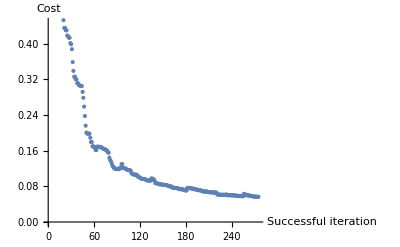

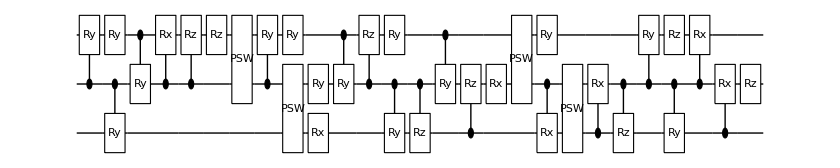

prob(0):None

dist_fid=0.27439

Compilation with automatically generated ansatz

$Aborted

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
toy0={};
Table[
conf=checkedConf[dev,unitary,5];
AppendTo[toy0,CompileCirc[conf,unitary,qubitsnum]]
,{5}];
```

## Small error: gate fidelity: 0.9999, T1=10^5,T2=100

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->100,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.9999,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{1,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.9999,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{1,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->1
};
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
toy1={};
Table[
conf=checkedConf[dev,unitary,5];
AppendTo[toy1,CompileCirc[conf,unitary,qubitsnum]]
,{5}];
```

## Mid error : 0.999, T1=10^5,T2=40

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->40,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.999,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{1,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.999,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{1,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->5
};
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
toy2={};
Table[
conf=checkedConf[dev,unitary,5];
AppendTo[toy2,CompileCirc[conf,unitary,qubitsnum]]
,{5}];
```